```mathematica
filesAR=FileNames["/home/carla/GDC/CONF/SED/GDC_Conf_AR_SED_ALL_Out/*.txt"];
dataAR=Map[Get[#]&, filesAR];
filesBR=FileNames["/home/carla/GDC/CONF/SED/GDC_Conf_BR_SED_ALL_Out/*.txt"];
dataBR=Map[Get[#]&, filesBR];
```

```mathematica
confAR=dataAR[[All,1]]
confBR=dataBR[[All,1]]
```

{{{0.00505051,1,198},{0.00393772,0.00505051,0.00111718},{0.6389,0.00505051,8.71422×10^-7,0.00111718}},{{0.00505051,1,198},{0.00397958,0.00505051,0.0010752},{0.650107,0.00505051,4.24797×10^-8,0.0010752}},{{0.00409836,1,244},{0.00348843,0.00409836,0.000612063},{0.740913,0.00409836,3.50848×10^-9,0.000612063}},{{0.00297619,1,336},{0.00263474,0.00297619,0.000342354},{0.79416,0.00297619,4.91853×10^-10,0.000342354}},{{0.00348432,1,287},{0.0031471,0.00348432,0.000338286},{0.823515,0.00348432,6.15835×10^-11,0.000338286}},{{1.,1,1},{1.,1.,0.000435964},{1,1.,9.9865×10^-14,0.000435964}}}

{{{0.00505051,28,5544},{0.00397958,0.00505051,0.0010752},{0.650107,0.00505051,1.18943×10^-6,0.0010752}},{{0.00409836,16,3904},{0.00348843,0.00409836,0.000612063},{0.740913,0.00409836,5.61357×10^-8,0.000612063}},{{0.00297619,5,1680},{0.00263474,0.00297619,0.000342354},{0.79416,0.00297619,2.45926×10^-9,0.000342354}},{{0.00297619,1,336},{0.0026388,0.00297619,0.000338286},{0.796357,0.00297619,7.20978×10^-11,0.000338286}},{{0.00348432,1,287},{0.0031497,0.00348432,0.000335676},{0.824758,0.00348432,2.86613×10^-11,0.000335676}}}

```mathematica
dojCHEVBKAR=confAR[[All,1]][[All,1]]
dojCHAR=confAR[[All,2]][[All,3]]
dojEVBKAR=confAR[[All,3]][[All,3]]

dojCHEVBKBR=confBR[[All,1]][[All,1]]
dojCHBR=confBR[[All,2]][[All,3]]
dojEVBKBR=confBR[[All,3]][[All,3]]
```

{0.00505051,0.00505051,0.00409836,0.00297619,0.00348432,1.}

{0.00111718,0.0010752,0.000612063,0.000342354,0.000338286,0.000435964}

{8.71422×10^-7,4.24797×10^-8,3.50848×10^-9,4.91853×10^-10,6.15835×10^-11,9.9865×10^-14}

{0.00505051,0.00409836,0.00297619,0.00297619,0.00348432}

{0.0010752,0.000612063,0.000342354,0.000338286,0.000335676}

{1.18943×10^-6,5.61357×10^-8,2.45926×10^-9,7.20978×10^-11,2.86613×10^-11}

```mathematica
(*sList={"S0","S1","S2","S3","S4","S5","S6","S7","S8"};
dojP=Labeled[#[[1]],#[[2]]]&/@Map[{doj[[#]],sList[[#]]}&,ran]*)

sList={3,4,5,6,7,8};
sList2={3.5,4.5,5.5,6.5,7.5};
ran=Range[Length[sList]];
ran2=Range[Length[sList2]];

dojAAR={#[[2]],#[[1]]}&/@Map[{N[dojCHAR[[#]]/dojCHEVBKAR[[#]]],sList[[#]]}&,ran]
dojABR={#[[2]],#[[1]]}&/@Map[{N[dojCHBR[[#]]/dojCHEVBKBR[[#]]],sList2[[#]]}&,ran2]
dojPCHAR={#[[2]],#[[1]]}&/@Map[{dojCHAR[[#]],sList[[#]]}&,ran]
dojPCHBR={#[[2]],#[[1]]}&/@Map[{dojCHBR[[#]],sList2[[#]]}&,ran2]
dojPEVBKAR={#[[2]],#[[1]]}&/@Map[{dojEVBKAR[[#]],sList[[#]]}&,ran]
dojPEVBKBR={#[[2]],#[[1]]}&/@Map[{dojEVBKBR[[#]],sList2[[#]]}&,ran2]
```

{{3,0.221202},{4,0.21289},{5,0.149343},{6,0.115031},{7,0.0970881},{8,0.000435964}}

{{3.5,0.21289},{4.5,0.149343},{5.5,0.115031},{6.5,0.113664},{7.5,0.0963389}}

{{3,0.00111718},{4,0.0010752},{5,0.000612063},{6,0.000342354},{7,0.000338286},{8,0.000435964}}

{{3.5,0.0010752},{4.5,0.000612063},{5.5,0.000342354},{6.5,0.000338286},{7.5,0.000335676}}

{{3,8.71422×10^-7},{4,4.24797×10^-8},{5,3.50848×10^-9},{6,4.91853×10^-10},{7,6.15835×10^-11},{8,9.9865×10^-14}}

{{3.5,1.18943×10^-6},{4.5,5.61357×10^-8},{5.5,2.45926×10^-9},{6.5,7.20978×10^-11},{7.5,2.86613×10^-11}}

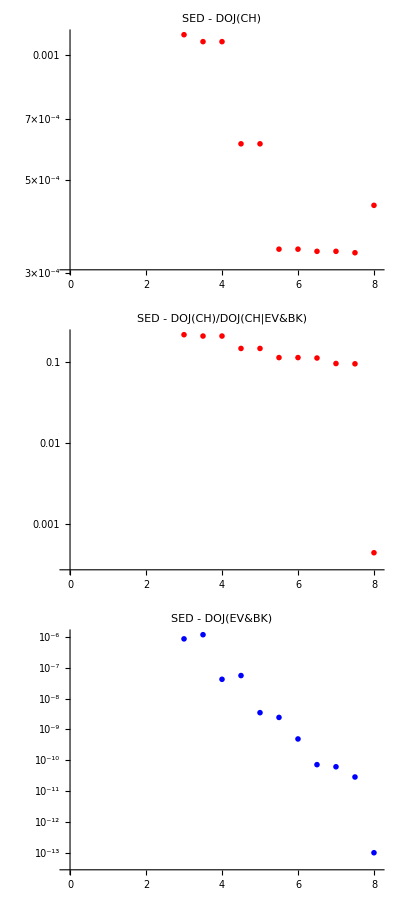

```mathematica
aPlot=ListLogPlot[{Union[dojAAR,dojABR]},  PlotLabel->"SED - DOJ(CH)/DOJ(CH|EV&BK)", PlotRange->{{-0.1,8.1},All}, PlotStyle-> {Red}, PlotRange->All, PlotMarkers->{{"A",12}},ImageSize->400];
chPlot=ListLogPlot[{Union[dojPCHAR,dojPCHBR]}, PlotRange->{{-0.1,8.1},All}, PlotStyle-> {Red}, PlotRange->All, PlotLabel->"SED - DOJ(CH)", PlotMarkers->{{"C",12}},ImageSize->400];
evbkPlot=ListLogPlot[{Union[dojPEVBKAR,dojPEVBKBR]},PlotRange->{{-0.1,8.1},All}, PlotStyle-> {Blue}, PlotRange->All, PlotLabel->"SED - DOJ(EV&BK)", PlotMarkers->{{"E",12}},ImageSize->400];
allPlot=ListLogPlot[{Union[dojPCHAR,dojPCHBR], Union[dojPEVBKAR,dojPEVBKBR]}, PlotLegends->{"DOJ(CH)","DOJ(EV&BK)"}, PlotRange->{{-0.1,8.1},All}, PlotStyle-> {Red, Blue}, PlotRange->All, PlotLabel->"SED - DOJ(CH),DOJ(EV&BK)", PlotMarkers->{{"C",12},{"E",12}},ImageSize->400];
plotsOut=Column[{chPlot,aPlot,evbkPlot}, ItemSize->35, Alignment->Center]
```

```mathematica
SetDirectory["/home/carla/GDC/CONF/SED/"];
Export["SED_CH_EVBK.jpeg",plotsOut,ImageResolution->200]
Put[Union[dojPCHAR,dojPCHBR],"SED_Z_APP.txt"]
Put[Union[dojAAR,dojABR],"SED_F_APP.txt"]
```

SED_CH_EVBK.jpeg

```mathematica
(*PlotParts=ListPlot[{Union[dojPAR,dojPBR], Union[zPAR,zPBR], Union[fPAR, fPBR]}, PlotLegends->{"DOJ","Z", "F"}, PlotStyle-> {Red, Blue, Yellow}, PlotRange->{0, 0.026},  PlotLabel->"SED - DOJ, Z, F - Zoomed In",  PlotMarkers->{{"D",12},{"Z",12},{"F",12}}]
Export["SED_Zoomed_In.jpeg",PlotParts,ImageSize->850]*)
```